```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/Users/stephaniekwan/Documents/SURF 2016/Palomar data/TSpec reductions/tspec.txt

LoadFile::sorted: Data sorted in increasing x order.

Read 8144 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

```mathematica
Undo[]
```

tspec.txt

n = 8144

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{1.044,1.351}

n= 2626

5518 points removed.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{1.0784,1.0892}

n= 75

2551 points removed.

```mathematica
LinearDifferencePlot[]
```

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{1.0782,1.0884}

n= 70

2556 points removed.

```mathematica
GaussianCFit[]
```

n = 70

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
0.0165049 | c= 
0.00451481 | 
σ_y_max= 
0.00121491 | σ_c= 
0.000274628 | 
μ= 
1.08239 | sigma= 
0.00039586 | 
σ_μ= 
0.0000335127 | σ_sigma= 
0.0000433762 | Std. deviation= 
0.002015

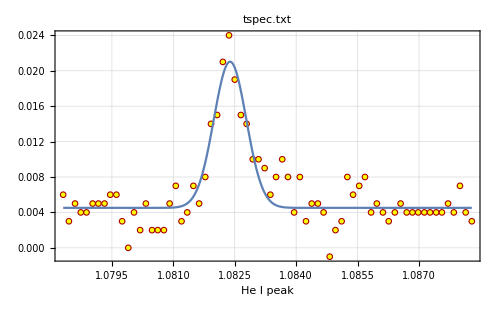
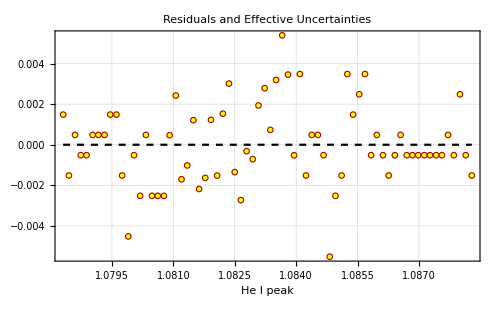
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
0.0165049 | c= 
0.00451481 | 
σ_y_max= 
0.00121491 | σ_c= 
0.000274628 | 
μ= 
1.08239 | sigma= 
0.00039586 | 
σ_μ= 
0.0000335127 | σ_sigma= 
0.0000433762 | Std. deviation= 
0.002015

```mathematica
LinearDifferencePlot[FrameLabel->{"He I peak"}]
```

```mathematica
Undo[]
```

tspec.txt

n = 2626

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{1.09,1.0962}

n= 43

2583 points removed.

```mathematica
GaussianCFit[]
```

n = 43

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
0.0143403 | c= 
0.00549301 | 
σ_y_max= 
0.00114548 | σ_c= 
0.000287788 | 
μ= 
1.0931 | sigma= 
0.000264796 | 
σ_μ= 
0.0000243091 | σ_sigma= 
0.0000245988 | Std. deviation= 
0.00167534

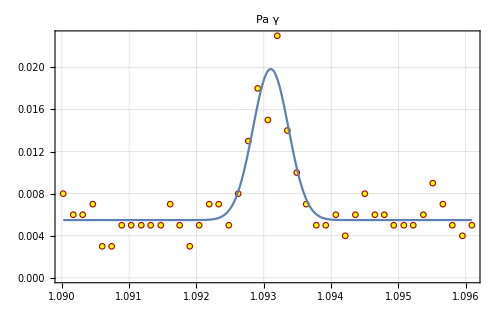
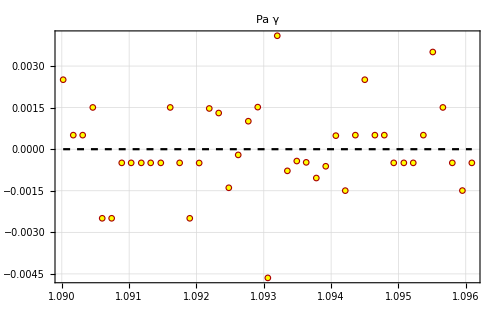
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
0.0143403 | c= 
0.00549301 | 
σ_y_max= 
0.00114548 | σ_c= 
0.000287788 | 
μ= 
1.0931 | sigma= 
0.000264796 | 
σ_μ= 
0.0000243091 | σ_sigma= 
0.0000245988 | Std. deviation= 
0.00167534

```mathematica
LinearDifferencePlot[PlotLabel->"Pa γ"]
```

```mathematica
Undo[]
```

tspec.txt

n = 2626

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{1.2774,1.2854}

n= 46

2580 points removed.

```mathematica
GaussianCFit[]
```

n = 46

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
0.0360744 | c= 
0.00773448 | 
σ_y_max= 
0.00170504 | σ_c= 
0.000349452 | 
μ= 
1.28103 | sigma= 
0.000261154 | 
σ_μ= 
0.0000135331 | σ_sigma= 
0.0000166814 | Std. deviation= 
0.00213072

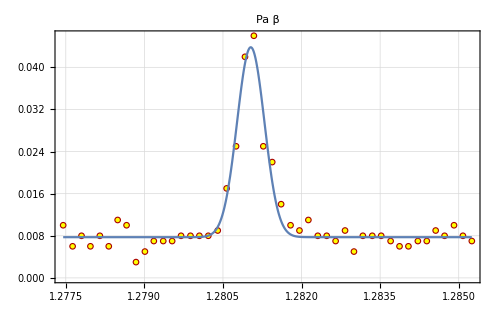
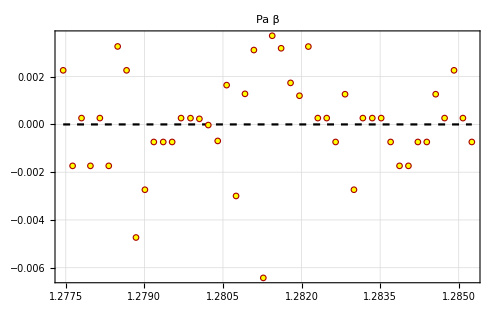
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
0.0360744 | c= 
0.00773448 | 
σ_y_max= 
0.00170504 | σ_c= 
0.000349452 | 
μ= 
1.28103 | sigma= 
0.000261154 | 
σ_μ= 
0.0000135331 | σ_sigma= 
0.0000166814 | Std. deviation= 
0.00213072

```mathematica
LinearDifferencePlot[PlotLabel->"Pa β"]
```

```mathematica
2 √(2 Log[2])*0.0002611
```

0.000614844

```mathematica
(* Find velocity by using FWHM and Doppler Shift, in km/s)
```

```mathematica
(0.000932*10*^-6)/(1.0824*10*^-6)*3*^5
```

258.315

```mathematica
(0.000624*10*^-6)/(1.0931*10*^-6)*3*^5
```

171.256

```mathematica
(0.000615*10*^-6)/(1.281*10*^-6)*3*^5
```

144.028

```mathematica
(* Uncertainty *)
```

```mathematica
3*^5 √(((1/1.0824)(0.000102))^2+((-0.000932/1.0824^2)(3.35*10^-5))^2)
```

28.2705

```mathematica
3*^5 √(((1/1.0931)(0.0000579))^2+((-0.000624/1.0931^2)(0.00002431))^2)
```

15.8906

```mathematica
3*^5 √(((1/1.281)(0.0000393))^2+((-0.000615/1.281^2)(0.0000135))^2)
```

9.20375

```mathematica
(* Blueshift of galaxy itself *)
```

```mathematica
(1.0819*10^4-10830.3398)/10830.3398*3*^5
```

-314.112

```mathematica
(1.0926*10^4-10938.1)/10938.1*3*^5
```

-331.868

```mathematica
(1.2805*10^4-12818.1)/12818.1*3*^5
```

-306.598

```mathematica
(* Resolution check *)
R := 2600
N[1.0819/R]
```

0.000416115

0.00416115 micron resolution. Convert to velocities in km/s

```mathematica
0.000423077/1.0819*3*^5
```

117.315

```mathematica
(* Correction for instrument FWHM *)
```

```mathematica
(* Instrument resolution: *)
```

```mathematica
res := 2600
```

```mathematica
(* He I line: FWHM corrected is, in microns:*)
```

```mathematica
heIPeak := 1.0824
heISigma :=0.000396
heISigmaUncertainty := 0.0000434
```

```mathematica
heIFWHM=√((2(√(2Log[2])heISigma))^2-(heIPeak/res)^2)
```

0.000834422

```mathematica
(* Convert to velocity/wind speed, in km/s *)
```

```mathematica
heIFWHM/heIPeak*3*^5
```

231.27

```mathematica
(* Pa gamma line: FWHM corrected is *)
```

```mathematica
paGammaPeak := 1.0931
paGammaSigma := 0.0002648
```

```mathematica
paGammaFWHM =√((2(√(2Log[2])paGammaSigma))^2-(paGammaPeak/res)^2)
```

0.000460507

```mathematica
√((2(√(2Log[2])paGammaSigma))^2-(paGammaPeak/res)^2)
```

```mathematica
paGammaFWHM/paGammaPeak*3*^5
```

126.386

```mathematica
(* Pa beta line *)
paBetaPeak := 1.281
paBetaSigma := 0.0002611
paBetaFWHM =√((2(√(2Log[2])paBetaSigma))^2-(paBetaPeak/res)^2)
```

0.000367814

```mathematica
paBetaFWHM/paBetaPeak*3*^5
```

86.139